# Rubrik (skriv projektets namn här)

## MA2001/MA2049 Envariabelanalys HT24

Rapportversion 1, inlämnad 2024 - 12 - 24

## Grupp

Förnamn1 Efternamn1

Förnamn2 Efternamn2

Förnamn3 Efternamn3

Förnamn4 Efternamn4

## Uppgifter

### Instruktioner

Varje deluppgift i projektet ska redovisas enligt nedan.

Krav: Filen ska klara “Ctrl-A” + “Shift-return” utan att lämna något felmeddelande.

Handledningar till Mathematica hittar du här: http://dixon.hh.se/mikael/links.shtml

Svensk rättstavning kan väljas i 
Format->Option inspector->Formatting options->Text content options
eller genom att köra:

```mathematica
CurrentValue[EvaluationNotebook[],DefaultNaturalLanguage]="Swedish";
```

### 1)

#### Problem

Förklaring av problemet.Vad ska göras? Ev referenser ska anges med nummer inom hakparenteser (se nedan). 
Exempel: Vid beräkningen av integralen

∫_0^π sin^2 ⅆx

utnyttjar vi formelncos 2x = cos^2 x-sin^2 x =1-2 sin^2 x från projektbeskrivningen[1].

#### Lösning

Redogörelse/lösningsförklaring och beräkningar med ev hänvisningar till nedanstående Mathematicakod.

Ev referenser anges också (se nedan).

Matematiska uttryck ska formateras korrekt. I en text används "Ctrl + (" för start av det matematiska uttrycket och "Ctrl + )" för slut (motsvarar dollartecknet $ i LATEX). 
Exempel: Med hjälp av  vi pq-formeln löser vi enkelt andragradsekvationen: x^2-2x=2⇔x_1=1+√3 eller x_2=1-√3.  Eftersom vi är ute efter den positiva roten är svaret på frågan 1+√3.

#### Mathematicakod

Utnyttjas Mathematica för beräkningar ska körbar kod visas här.

Grafen till TraditionalForm`f(x):

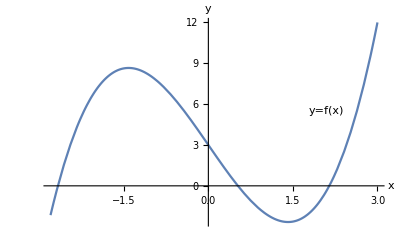

Derivatan: f'(x) = -6+3 x^2

Stationära punkter (nollställena till f'(x)): x1 = -√2 och x2 = √2.

Motsvarande funktionsvärden: f(x1) = 3+4 √2 och f(x2) = 3-4 √2

```mathematica
Remove["Global`*"]
f[x_]:=x^3-6x+3;
Print["Grafen till TraditionalForm`f(x):"]
Plot[f[x],{x,-2.8,3},AxesLabel->{x,y},Epilog->{Text["y=f(x)",{2.1,5.5}]}]
(* Nollställena till f'(x) *)
nollst=Solve[f'[x]==0,x];
x1=nollst[[1,1,2]];
x2=nollst[[2,1,2]];
Print["Derivatan: f'(x) = ",f'[x]];Print["Stationära punkter (nollställena till f'(x)): x1 = ",x1," och " ,"x2 = ",x2,"."]
Print["Motsvarande funktionsvärden: f(x1) = ",f[x1]," och ","f(x2) = ",f[x2]]
```

#### Slutsatser och resultat

Vad blir resultatet/svaret? Är resultatet rimligt? Vilka slutsatser kan dras av ovanstående beräkningar?

## Referenser

Här anges vilka källor som utnyttjats och som refereras till i rapporten. Ex:

[1] Projektuppgift 1.5 hp,  http://dixon.hh.se/mikael/teaching/analys/project.shtml

[2] J. Månsson och P. Nordbeck, Endimensionell analys, Studentlitteratur (2011)

[3] Wikipedia, Capacitor, https://en.wikipedia.org/wiki/Capacitor